# Analysis of pattern wavelength and oscillation period for the switch model in rot. symm. spherocylinder geometry

Params used for 2D rot. symm. simulation analysed here;
Note that the nonlinear reaction rates are scaled such that the fast-growth wild-type concentrations are 1000 um^-3.

```mathematica
params={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->0.3,
kdD->0.0015,
kdEr->1.5,
kdEl->10^-5,
kde->1,
λ->5,
μ->20,
L->50,
he->0.5,
T->3000
};
```

## Setup

## Import of simulation data from Comsol

Import functions to load the data from Comsol simulations

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->"InitializationCell"
];
```

## Analyze pattern kymographs

### Pattern test

Classify patterns based on morphological analysis.
We distinguish pattern formation driven by a dynamical instability from a parameter set that does not lead to dynamic pattern formation by testing for homogeneity in the middle of the domain (neglecting a third of the domain on the left and right).
The reason is that the non-uniform bulk-boundary ratio at the cell poles already leads to inhomogeneity of the stationary state without any pattern-forming, dynamical instability of the stationary state (cf. Thalmeier, et al., PNAS 2015)

```mathematica
ClearAll[testPatternMorphological];
Options[testPatternMorphological] = {"TimePoints" -> 200, "BoundaryPoints" -> 1};
testPatternMorphological[kymo_, opts : OptionsPattern[]] := Block[{
testField,
timeavg,
psAvg,psMax,wavelength,relContrast,period,
avgTF, max, min,outPoints,maxIn,minIn,
morphComp,
nHighDensClusters
},
testField = kymo[[-Min[OptionValue["TimePoints"],Length@kymo];;,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"]]];
{avgTF, max, min} = {Mean@#, Max@#, Min@#} &@Flatten[testField];
testField = (testField - avgTF);
timeavg=Mean[testField];

outPoints=Floor[Length[testField[[1]]]/3];
{maxIn,minIn}={Max@#,Min@#}&@Flatten[avgTF+testField[[All,outPoints;;-outPoints]]];

If[Abs[(maxIn-minIn)/minIn] < 0.05,
{I,0},(*no pattern formation*)
psAvg=Mean[Abs[Fourier[Join[#,Reverse@#]-Mean@#]&/@testField]^2];
psMax=SortBy[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
wavelength=Quiet[Check[2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],Length[testField[[1]]],Power::infy],Power::infy];
psAvg=Abs[Fourier[timeavg]]^2;
relContrast=2#/(avgTF+#)&@(2 Sqrt[Max@psAvg[[3;;-2]]/Length[timeavg]]);
psAvg=Mean[Abs[Fourier[#-Mean@#]&/@Transpose@testField]^2];
psMax=SortBy[Transpose@{2Pi /Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
period=Quiet[Check[ 2Pi/Min[psMax[[1]],2Pi-psMax[[1]]],OptionValue["TimePoints"],Power::infy],Power::infy];

If[period>Min[OptionValue["TimePoints"],Length@kymo]/2,
{2I,0},(*too short time window*)

morphComp=MorphologicalComponents[Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,

Print[Colorize@MorphologicalComponents[Binarize@Image@kymo[[-Min[400,Length@kymo];;;;4,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"];;4]]]];
Print["period: ",N@period,", wavelength: ",N@wavelength];

morphComp=MorphologicalComponents[ColorNegate@Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,
{5I,relContrast},
Print["inverted SW"];
{4I,relContrast}(*inverted SWs*)
],(*TWs*)

{6I,relContrast}(*SWs*)
]
]
]
];
```

Print intermediate results along the way

```mathematica
ClearAll[testPatternMorphologicalPrint];
Options[testPatternMorphologicalPrint] = {"TimePoints" -> 200, "BoundaryPoints" -> 1};
testPatternMorphologicalPrint[kymo_, opts : OptionsPattern[]] := Block[{
testField,
timeavg,
psAvg,psMax,wavelength,relContrast,period,
avgTF, max, min,outPoints,maxIn,minIn,
morphComp,
nHighDensClusters
},
testField = kymo[[-Min[OptionValue["TimePoints"],Length@kymo];;,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"]]];
{avgTF, max, min} = {Mean@#, Max@#, Min@#} &@Flatten[testField];
testField = (testField - avgTF);
timeavg=Mean[testField];

outPoints=Floor[Length[testField[[1]]]/3];
{maxIn,minIn}={Max@#,Min@#}&@Flatten[avgTF+testField[[All,outPoints;;-outPoints]]];

If[Abs[(maxIn-minIn)/minIn] < 0.05,
{I,0},(*no pattern formation*)
psAvg=Mean[Abs[Fourier[Join[#,Reverse@#]-Mean@#]&/@testField]^2];
psMax=SortBy[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
Print["Time-averaged structure factor:"];
Print[ListLinePlot[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},PlotRange->All]];
wavelength=Quiet[Check[2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],Length[testField[[1]]],Power::infy],Power::infy];
psAvg=Abs[Fourier[timeavg]]^2;
relContrast=2#/(avgTF+#)&@(2 Sqrt[Max@psAvg[[3;;-2]]/Length[timeavg]]);
psAvg=Mean[Abs[Fourier[#-Mean@#]&/@Transpose@testField]^2];
psMax=SortBy[Transpose@{2Pi /Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
Print["Spatially averaged power spectrum:"];
Print[ListLinePlot[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},PlotRange->All]];
period=Quiet[Check[ 2Pi/Min[psMax[[1]],2Pi-psMax[[1]]],OptionValue["TimePoints"],Power::infy],Power::infy];

If[period>Min[OptionValue["TimePoints"],Length@kymo]/2,
{2I,0},(*too short time window*)

morphComp=MorphologicalComponents[Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;
Print[ImageReflect@ImageResize[Colorize@morphComp,{500,500}]];

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,

Print["period: ",N@period,", wavelength: ",N@wavelength];

morphComp=MorphologicalComponents[ColorNegate@Binarize[Image@testField]];
nHighDensClusters=Max@morphComp;
Print[ImageReflect@ImageResize[Colorize@morphComp,{500,500}]];

If[nHighDensClusters<(Length[kymo[[1]]]/wavelength+2)Min[OptionValue["TimePoints"],Length@kymo]/period,
{5I,relContrast},
Print["inverted SW"];
{4I,relContrast}(*inverted SWs*)
],(*TWs*)

Print["period: ",N@period,", wavelength: ",N@wavelength];
{6I,relContrast}(*SWs*)
]
]
]
];
```

### Pattern test sweep

```mathematica
ClearAll[testSweepMorph];
Options[testSweepMorph]=Options[testPatternMorphological];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
testSweepMorph[filename_,opts:OptionsPattern[]]:=Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
valuesVariedParams=Import[filename,{"/ValuesVariedParameters"}]
},
Reap[
Do[Block[{
group=StringJoin["/",Riffle[parameterNames,StringTrim[#,"."]&/@{ToString[vps[[1]]],ToString[vps[[2]]]}]],
data,
analysis
},
data=Quiet[Total[Import[filename,{{group<>"/ud",group<>"/ude"}}]]];
If[!MatrixQ[data],Continue[]];
analysis=testPatternMorphological[data,Sequence@@(List@opts)];
If[analysis[[1]]==4I||analysis[[1]]==5I,Print[Log10@vps];];
Sow@Join[vps,{analysis}];

],{vps,valuesVariedParams}];
][[-1,1]]
];
```

```mathematica
ClearAll[testSweepMultipleFilesMorph];
Options[testSweepMultipleFilesMorph]=Options[testPatternMorphological];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
testSweepMultipleFilesMorph[filenameList_,opts:OptionsPattern[]]:=
Flatten[
Reap[Do[
Sow@testSweepMorph[filename,Sequence@@(List@opts)];,
{filename,filenameList}]][[-1,1]],
1]
```

### Plot kymographs

```mathematica
ClearAll[dataKymo];
(*valuesVariedParameters is one parameter set here*)
dataKymo[filenameList_,valuesVariedParameters_]:=Block[{
kymo
},
Reap[Do[
Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
group
},
group=StringJoin["/",Riffle[parameterNames,StringTrim[#,"."|RegularExpression["\\.0*"]]&/@{ToString@SetPrecision[#[[1]],5],ToString@SetPrecision[#[[2]],5]}&@Evaluate[valuesVariedParameters]]];

If[MemberQ[Import[filename,"Datasets"],group<>"/ud"],
Sow[Import[filename,{{group<>"/ud",group<>"/ude"}}]]];
],
{filename,filenameList}];][[-1,1,1]]
];
```

### Wavelength & period analysis

```mathematica
ClearAll[analyzeKymo];
Options[analyzeKymo]={"TimePoints"->200,"BoundaryPoints"->25,"DX"->0.5,"DT"->4};
analyzeKymo[kymo_,opts:OptionsPattern[]]:=Block[{
testField,
timeavg,
psAvg,psMax,wavelength,relContrast,period,
avgTF, max, min,outPoints,maxIn,minIn,
dx=OptionValue["DX"],
dt=OptionValue["DT"]
},
testField = kymo[[-Min[OptionValue["TimePoints"],Length@kymo];;,OptionValue["BoundaryPoints"];;-OptionValue["BoundaryPoints"]]];
{avgTF, max, min} = {Mean@#, Max@#, Min@#} &@Flatten[testField];
testField = (testField - avgTF);
timeavg=Mean[testField];

outPoints=Floor[Length[testField[[1]]]/3];
{maxIn,minIn}={Max@#,Min@#}&@Flatten[avgTF+testField[[All,outPoints;;-outPoints]]];

If[Abs[(maxIn-minIn)/minIn] < 0.05,
I,

psAvg=Mean[Abs[Fourier[#-Mean@#]&/@testField]^2];
psMax=SortBy[Transpose@{2Pi/Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
wavelength=dx Quiet[Check[2Pi /Min[psMax[[1]],2Pi-psMax[[1]]],Length[testField[[1]]],Power::infy],Power::infy];
psAvg=Abs[Fourier[timeavg]]^2;
relContrast=2#/(avgTF+#)&@(2 Sqrt[Max@psAvg[[3;;-2]]/Length[timeavg]]);
psAvg=Mean[Abs[Fourier[#-Mean@#]&/@Transpose@testField]^2];
psMax=SortBy[Transpose@{2Pi /Length[psAvg]*(Range[Length@psAvg]-1),psAvg},#[[2]]&][[-1]];
period=dt Quiet[Check[ 2Pi/Min[psMax[[1]],2Pi-psMax[[1]]],OptionValue["TimePoints"],Power::infy],Power::infy];
{
relContrast,
wavelength,
period
}
]
];
```

```mathematica
ClearAll[analysisSweep];
Options[analysisSweep]=Options[analyzeKymo];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
analysisSweep[filename_,opts:OptionsPattern[]]:=Block[{
parameterNames=Import[filename,{"Attributes","/"}]["VariedParameters"],
valuesVariedParams=Import[filename,{"/ValuesVariedParameters"}]
},

Reap[
Do[Block[{
group=StringJoin["/",Riffle[parameterNames,StringTrim[#,"."]&/@{ToString[vps[[1]]]}]],
data,
analysis
},
data=Quiet[Total[Import[filename,{{group<>"/ud",group<>"/ude"}}]]];
If[!MatrixQ[data],Continue[]];
analysis=analyzeKymo[data,Sequence@@(List@opts)];

Sow@Join[vps,{analysis}];

],{vps,valuesVariedParams}];
][[-1,1]]
];
```

```mathematica
ClearAll[analysisSweepMultipleFiles];
Options[analysisSweepMultipleFiles]=Options[analyzeKymo];
(*variedParams should have the same layout as the interation-variable specification in a multidimensional table*)
analysisSweepMultipleFiles[filenameList_,opts:OptionsPattern[]]:=
Flatten[
Reap[Do[
Sow@analysisSweep[filename,Sequence@@(List@opts)];,
{filename,filenameList}]][[-1,1]],
1]
```

## Import Comsol data export and save as hdf5 file

Assuming that Comsol .txt export files are saved in the same directory as this notebook.

```mathematica
data=Import[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoE_13500-wavelengthPeriod.txt","ComsolSweep1DMultiComp"];
```

```mathematica
hdf5ExportSweep1D[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoE_13500-wavelengthPeriod.h5",data,{}];
```

```mathematica
data2=Import[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoD_1500-wavelengthPeriod.txt","ComsolSweep1DMultiComp"];
```

```mathematica
hdf5ExportSweep1D[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoD_1500-wavelengthPeriod.h5",data2,{}];
```

## Analyze wavelength and period

```mathematica
filenames={NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoE_13500-wavelengthPeriod.h5",
NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-rhoD_1500-wavelengthPeriod.h5"};
```

```mathematica
analysisWPrhoDsweep=analysisSweepMultipleFiles[{filenames[[1]]},"TimePoints"->500,"BoundaryPoints"->1,"DX"->0.2,"DT"->2];
```

```mathematica
analysisWPrhoEsweep=analysisSweepMultipleFiles[{filenames[[2]]},"TimePoints"->500,"BoundaryPoints"->1,"DX"->0.2,"DT"->2];
```

#### Wavelength

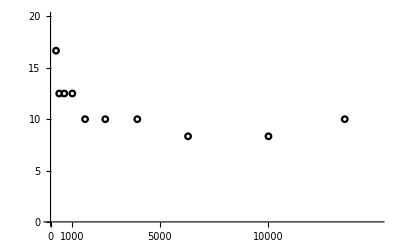

```mathematica
ListPlot[{#[[1]],#[[2,2]]}&/@Select[analysisWPrhoEsweep,(ListQ@#[[2]])&],
PlotRange->{{0,15000},{0,20}},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
Ticks->{{0,1000,5000,10000},{0,5,10,15,20}}
]
```

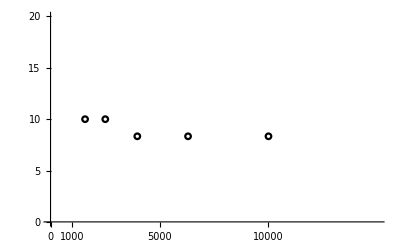

```mathematica
ListPlot[{#[[1]],#[[2,2]]}&/@Select[analysisWPrhoDsweep,(ListQ@#[[2]])&],
PlotRange->{{0,15000},{0,20}},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
Ticks->{{0,1000,5000,10000},{0,5,10,15,20}}
]
```

#### Period

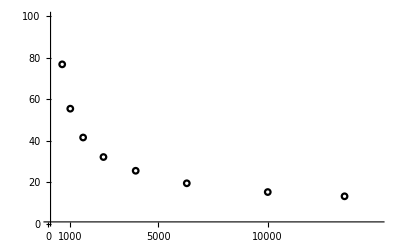

```mathematica
ListPlot[{#[[1]],#[[2,3]]}&/@Select[analysisWPrhoEsweep,(ListQ@#[[2]])&],
PlotRange->{{100,15000},{1,100}},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
Ticks->{{0,1000,5000,10000},{0,20,40,60,80,100}}
]
```

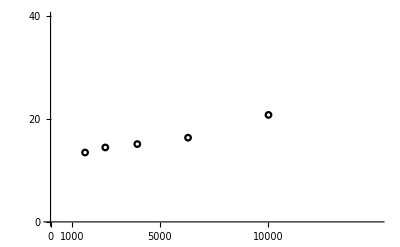

```mathematica
ListPlot[{#[[1]],#[[2,3]]}&/@Select[analysisWPrhoDsweep,(ListQ@#[[2]])&],
PlotRange->{{0,15000},{0,40}},
PlotMarkers->{Graphics[{Black,Circle[]}],0.04},
Ticks->{{0,1000,5000,10000},{0,20,40}}
]
```